## Modelo contínuo do sistema

```mathematica
A = {{-435.7,-5067},{1,0}};
```

```mathematica
B={{3264000},{0}};
```

```mathematica
Cs={{0,1}};
```

```mathematica
Ds={{0}};
```

```mathematica
SS=StateSpaceModel[{A,B,Cs,Ds}]
```

(-435.7 | -5067 | 3264000
1 | 0 | 0
0 | 1 | 0)_^𝒮

## Modelo discreto do sistema

```mathematica
SSd = ToDiscreteTimeModel[SS,Ts,Method->"ForwardRectangularRule"]
```

(1-435.7 Ts | -5067 Ts | 3264000 Ts
Ts | 1 | 0
0 | 1 | 0)_Ts^𝒮

## Analisando a estabilidade do sistema

```mathematica
roots = Solve[TransferFunctionModel[SSd][[1]][[2]]==0,z ]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{z→0.05 (20.-8474.85 Ts)},{z→0.05 (20.-239.155 Ts)}}

### Primeiro pólo do sistema em função do sampling time

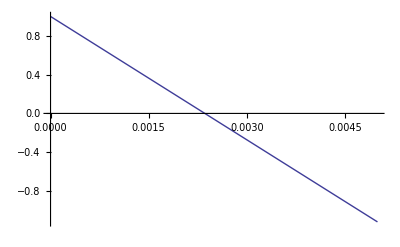

```mathematica
Plot[z/.(roots)[[1]],{Ts,0,0.005}]
```

### Segundo pólo do sistema em função do sampling time

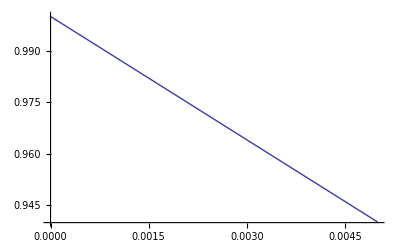

```mathematica
Plot[z/.(roots)[[2]],{Ts,0,0.005}]
```